```mathematica
CellularAutomaton[30,{1,0,0,0,0,1},2]
```

{{1,0,0,0,0,1},{0,1,0,0,1,1},{0,1,1,1,1,0}}

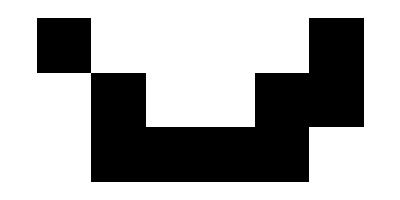

```mathematica
ArrayPlot[{{1,0,0,0,0,1},{0,1,0,0,1,1},{0,1,1,1,1,0}}]
```

```mathematica
ArrayPlot[CellularAutomaton[30,RandomInteger[1,100],100]]
```

-Graphics-

```mathematica
RandomInteger[1,100]
```

{1,1,1,1,0,1,0,0,1,1,1,1,0,1,1,0,1,0,1,1,1,0,1,0,1,1,1,0,0,0,1,0,0,1,0,1,1,0,0,1,1,0,0,0,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,1,0,1,1,0,1,0,0,1,0,0,1,0,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1}

```mathematica
RandomInteger[2,100]
```

{2,0,1,2,1,2,1,1,2,2,2,0,0,2,0,2,2,0,0,1,1,1,0,2,2,0,0,1,1,1,0,2,0,0,2,2,1,2,0,1,0,1,2,1,1,2,0,0,1,2,2,2,2,0,2,2,1,2,1,1,2,2,1,1,0,2,2,0,2,1,0,1,2,1,0,2,2,2,0,2,0,2,1,1,2,2,0,0,0,2,2,1,2,0,2,2,1,0,0,1}

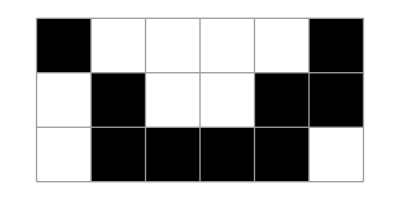

```mathematica
ArrayPlot[CellularAutomaton[30,{1,0,0,0,0,1},2],Mesh->All]
```

```mathematica
CellularAutomaton[90,{{1,1},0},2]
```

{{0,0,1,1,0,0},{0,1,1,1,1,0},{1,1,0,0,1,1}}

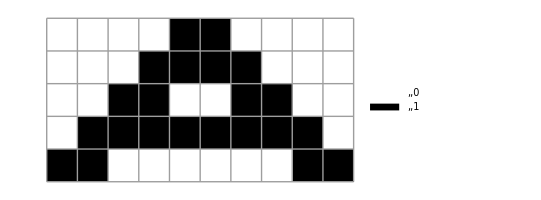

```mathematica
ArrayPlot[CellularAutomaton[90,{{1,1},0},4],Mesh->All,PlotLegends->Automatic]
```

```mathematica
ArrayPlot[CellularAutomaton[90,{{1,1},0},100]]
```

-Graphics-

```mathematica
CellularAutomaton[30,{{{{1},{-2}},{{1},{2}}},0},2]
```

{{0,0,1,0,0,0,1,0,0},{0,1,1,1,0,1,1,1,0},{1,1,0,0,0,1,0,0,1}}

```mathematica
CellularAutomaton[30,{{{{1},{-4}},{{1},{4}}},0},2]
```

{{0,0,1,0,0,0,0,0,0,0,1,0,0},{0,1,1,1,0,0,0,0,0,1,1,1,0},{1,1,0,0,1,0,0,0,1,1,0,0,1}}

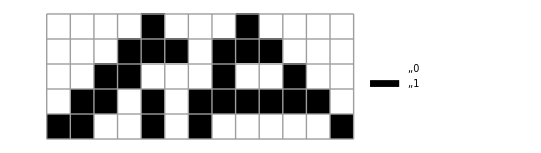

```mathematica
ArrayPlot[CellularAutomaton[30,{{{{1},{-2}},{{1},{2}}},0},4],Mesh->All,PlotLegends->Automatic]
```

```mathematica
ArrayPlot[CellularAutomaton[90,{{{{1},{-1}},{{1},{10}}},0},100]]
```

-Graphics-

```mathematica
arr=UpperTriangularize[ConstantArray[1,{9,9}]];
arr=Append[arr,ConstantArray[0,9]]
```

{{1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1},{0,0,1,1,1,1,1,1,1},{0,0,0,1,1,1,1,1,1},{0,0,0,0,1,1,1,1,1},{0,0,0,0,0,1,1,1,1},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0}}

```mathematica
rule = CellularAutomaton[{14,{2,1},{1,1}},Partition[#,3],1]&/@arr
```

{{{{1,1,1},{1,1,1},{1,1,1}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,1,1},{1,1,1},{1,1,1}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,1},{1,1,1},{1,1,1}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{1,1,1},{1,1,1}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,1,1},{1,1,1}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,1},{1,1,1}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{1,1,1}},{{1,1,1},{1,1,1},{1,1,1}}},{{{0,0,0},{0,0,0},{0,1,1}},{{1,1,1},{1,1,1},{1,1,1}}},{{{0,0,0},{0,0,0},{0,0,1}},{{1,1,1},{1,1,1},{1,1,1}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

```mathematica
FromDigits[rule,2]
```

{{{512,768,896},{960,992,1008},{1016,1020,1022}},{{14,14,14},{14,14,14},{14,14,14}}}

```mathematica
Table[ArrayPlot[Partition[arr[[i]],3],ImageSize->90,Mesh->All]->ArrayPlot[{{rule[[i]]}},ImageSize->20],{i,1,10}]
```

{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}

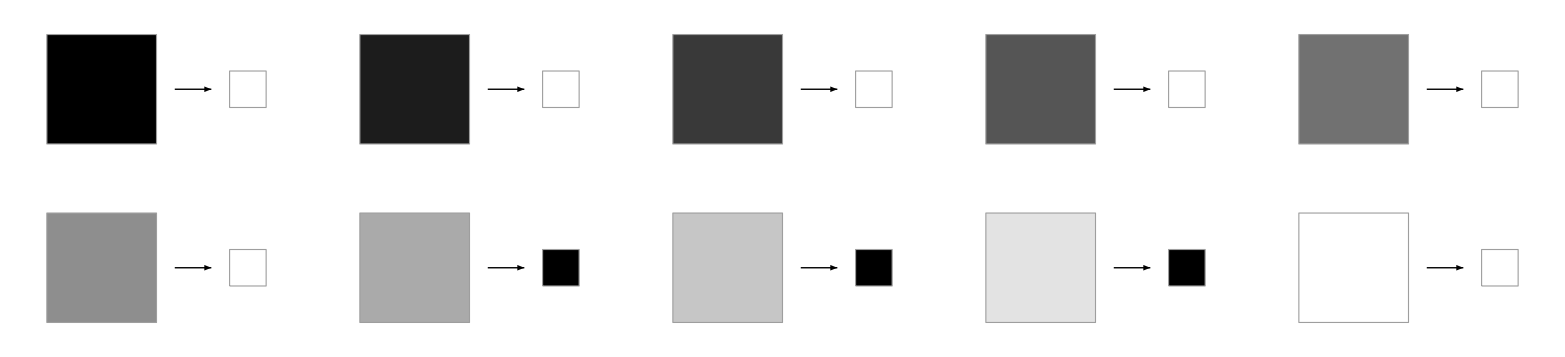

```mathematica
RulePlot[CellularAutomaton[{14,{2,1},{1,1}}]]
```